## Figures for Berry's Construction

Nicholas Wheeler
March 2018

### Figure 1

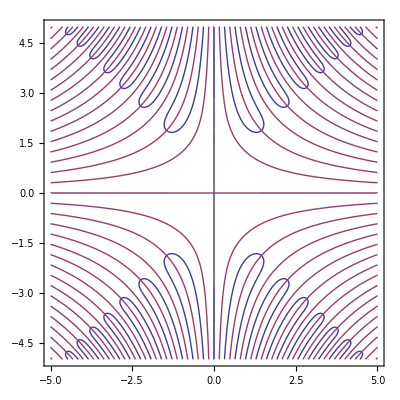

```mathematica
ContourPlot[{Re[Erf[x+ⅈ y]]==0,Im[Erf[x+ⅈ y]]==0},{x,-5,5},{y,-5,5},PlotPoints->100]
```

The null curves of real part (red) and imaginary part (blue) of Erf[x+ⅈy].  Orthogonality at points of intersection follows from analyticity (i.e., from the Cauchy-Riemann equations).

### Figures 2

```mathematica
ContourPlot[{Re[Erf[x+ⅈ y]]},{x,-5,5},{y,-5,5}]

ContourPlot[{Im[Erf[x+ⅈ y]]},{x,-5,5},{y,-5,5},PlotPoints->50]
```

-Graphics-

-Graphics-

### Figures 3

```mathematica
Plot3D[{Re[Erf[x+ⅈ y]]},{x,-5,5},{y,-5,5},PlotRange->{{-5,5},{-5,5},{-10,10}},PlotPoints->50]

Plot3D[{Im[Erf[x+ⅈ y]]},{x,-5,5},{y,-5,5},PlotRange->{{-5,5},{-5,5},{-10,10}},PlotPoints->50]
```

-Graphics3D-

-Graphics3D-

In the flat parts of the top figure the real part of Erf[x+ⅈy]is found never  to deviate by more than a few parts in a thousand from the value 1. In the bottom figure the flat portions of the imaginary part remain similarly close to the value 0. It is the flat parts of these figures that give rise to the condition b ⩽ b_max=2.

### Figure 4

```mathematica
Plot3D[{Abs[Erf[x+ⅈ y]]},{x,-5,5},{y,-5,5},PlotRange->{{-5,5},{-5,5},{-10,10}},PlotPoints->50]
```

-Graphics3D-

### Figure 5

Yet another demonstration of how abrupt  and extreme is the stratospheric ascent at the edge of the flat desert:

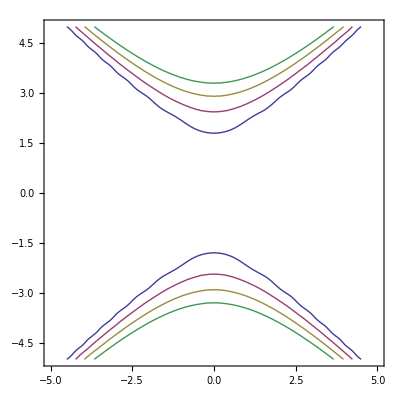

```mathematica
ContourPlot[{Abs[Erf[x+ⅈ y]]==10,Abs[Erf[x+ⅈ y]]==100,Abs[Erf[x+ⅈ y]]==1000,Abs[Erf[x+ⅈ y]]==10000},{x,-5,5},{y,-5,5},PlotPoints->50]
```

### Figures 6

```mathematica
X[x_,ν_,b_]:=(2 √ν (Cos[1/2 ArcTan[x/(2 ν)]]+(b/2+x/(2 ν)) Sin[1/2 ArcTan[x/(2 ν)]]))/((1+x^2/(4 ν^2))^(1/4))
Y[x_,ν_,b_]:=(2 √ν ((b/2+x/(2 ν)) Cos[1/2 ArcTan[x/(2 ν)]]-Sin[1/2 ArcTan[x/(2 ν)]]))/((1+x^2/(4 ν^2))^(1/4))
Z[x_,ν_,b_]:=X[x,ν,b]+ⅈ Y[x,ν,b]
```

```mathematica
ℰ[x_,ν_,b_]:=(Erf[Z[x,ν,b]]+Erf[Z[x,ν,-b]])/2
```

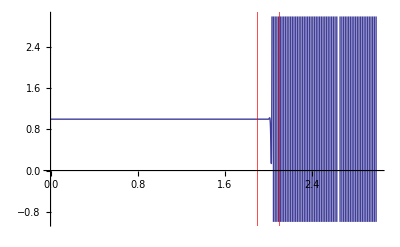

```mathematica
Plot[Re[ℰ[2,50,b]],{b,0,3},PlotRange->{{0,3},{-1,3}},
GridLines->{{{1.9,Red},{2.1,Red}},{}}]
```

```mathematica
ℰ[2,50,1.9]
ℰ[2,50,2.1]
```

1.-7.1789×10^-11 ⅈ

1.04841×10^7+1.68925×10^7 ⅈ

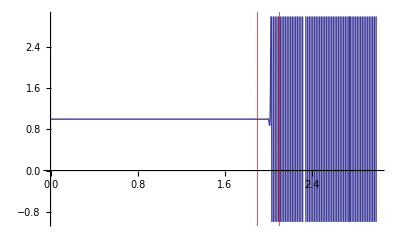

```mathematica
Plot[Re[ℰ[3,50,b]],{b,0,3},PlotRange->{{0,3},{-1,3}},
GridLines->{{{1.9,Red},{2.1,Red}},{}}]
```

```mathematica
ℰ[3,50,1.9]
ℰ[3,50,2.1]
```

1.+6.22934×10^-11 ⅈ

-1.77941×10^7+792137. ⅈ

Large values of ν can produce numbers so large that they exceed the capacity of the grapic command:

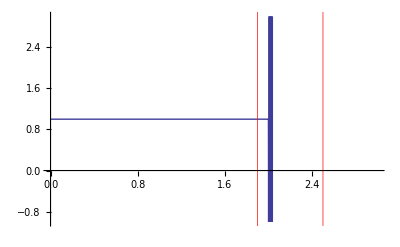

```mathematica
Plot[Re[ℰ[2,5000,b]],{b,0,3},PlotRange->{{0,3},{-1,3}},
GridLines->{{{1.9,Red},{2.5,Red}},{}}]
```

```mathematica
ℰ[2,5000,1.9]
ℰ[2,5000,2.5]
```

1.+3.74093521617816×10^-850 ⅈ

8.44617478171103×10^4882-9.14825937535729×10^4882 ⅈ

### Figure 7

```mathematica
ErfFunction=ContourPlot[{Re[Erf[x+ⅈ y]]==0,Im[Erf[x+ⅈ y]]==0},{x,13,16},{y,13,16}, PlotPoints->50];

DataPoints=Graphics[{PointSize[Large],{Red,Point[{14.2772,13.5744}]},
{Red,Point[{14.2913,14.9884}]},
{Blue,Point[{14.3451,13.6426}]},
{Blue,Point[{14.3663,15.0563}]}}];

bLine2=ParametricPlot[{X[2,50,b],Y[2,50,b]},{b,0,3},AspectRatio->Automatic,PlotStyle->{Red}];
bLine3=ParametricPlot[{X[3,50,b],Y[3,50,b]},{b,0,3},AspectRatio->Automatic,PlotStyle->{Blue}];
```

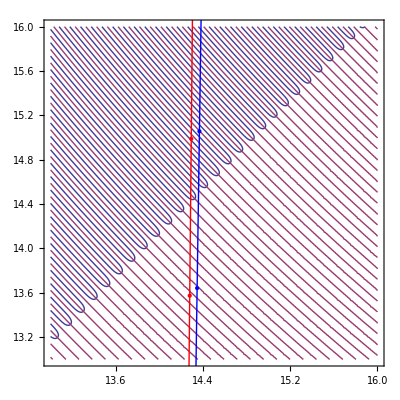

```mathematica
Show[ErfFunction,DataPoints,bLine2,bLine3]
```

### Figures 8

```mathematica
𝔹[x_,ν_,b_]:=1/(√(1+ⅈ ξ))Exp[(b^2 x ξ)/(2(1+ξ^2))]Exp[ⅈ x(1+b^2/(2(1+ξ^2)))]/.ξ->x/(2ν)
```

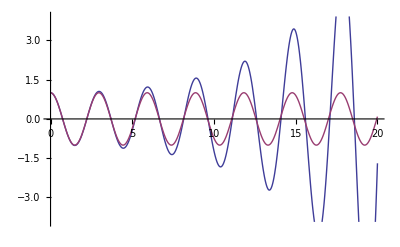

```mathematica
ν=100;
b=1.5;
Plot[{Re[𝔹[x,ν,b]],Cos[x(1+b^2/2)]},{x,0,20}]
```

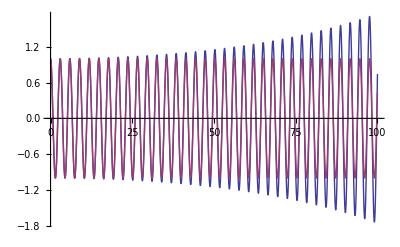

```mathematica
ν=10000;
b=1.5;
Plot[{Re[𝔹[x,ν,b]],Cos[x(1+b^2/2)]},{x,0,100}]
```

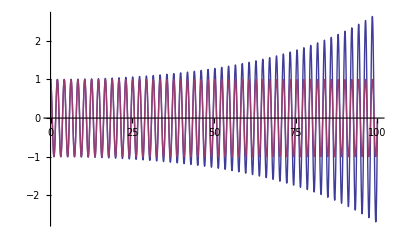

```mathematica
ν=10000;
b=2;
Plot[{Re[𝔹[x,ν,b]],Cos[x(1+b^2/2)]},{x,0,100}]
```

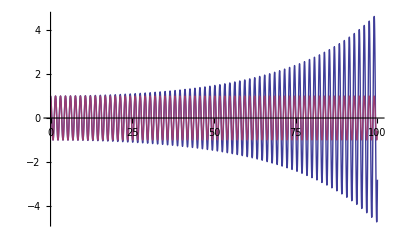

```mathematica
ν=10000;
b=2.5;
Plot[{Re[𝔹[x,ν,b]],Cos[x(1+b^2/2)]},{x,0,100}]
```

The final figure, though qualititively similar to the others, cannot illustrate superoscillation because the assumption b = 2.5 > b_max= 2 introduces terms with wavenumber > 1 into its construction.

### Figure 9: Locus of saddlepoints, in the case b = b_max

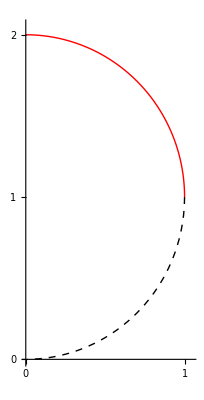

```mathematica
b=2.0;
SemicircleSegment=ParametricPlot[{(b ξ)/(1+ξ^2),b/(1+ξ^2)},{ξ,0,1},PlotRange->{{0,1.05},{0,2.05}},PlotStyle->{Thick,Red},Ticks->{{0,1},{0,1,2}}];
SemicircleComplete=ParametricPlot[{(b ξ)/(1+ξ^2),b/(1+ξ^2)},{ξ,1,200},PlotRange->{{0,1.05},{0,2.05}},PlotStyle->{Dashed,Thick,Black},Ticks->{{0,1},{0,1,2}}];
Show[SemicircleSegment,SemicircleComplete]
```

The red section is produced as ξ ranges from 0 to 1.

### Figure 10: "Local wavenumber" 𝒦 in the case b = b_max

```mathematica
𝒦[b_,ξ_]:=1+1/2 b^2(1-ξ^2)/((1+ξ^2)^2)
```

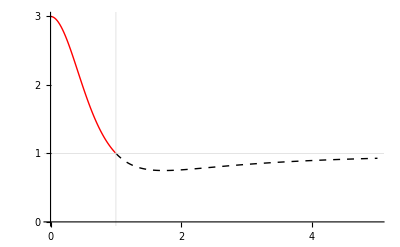

```mathematica
LocalWavenumberSegment=Plot[𝒦[2,ξ],{ξ,0,1},PlotRange->{{0,5},{0,3}},GridLines->{{1},{1}},PlotStyle->{Thick,Red},Ticks->{{0,1,2,3,4,5},{0,1,2,3}}];
 LocalWavenumberComplete=Plot[𝒦[2,ξ],{ξ,1,5},PlotRange->{{0,5},{0,3}},GridLines->{{1},{1}},PlotStyle->{Thick,Dashed,Black},Ticks->{{0,1,2,3,4,5},{0,1,2,3}}];

Show[ LocalWavenumberSegment, LocalWavenumberComplete]
```

Only for ξ < 1 does 𝒦  have a superoscillatory value > 1, and that value is bounded in the case b_max by 3, as shown. The red portion of this curve can be identified with the red portion of Figure 9.

### Figures 11

These are reconstructions of Berry's Figures 3a, 3b & 3c.

#### Figure 11a

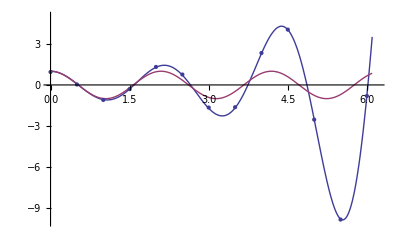

```mathematica
b=2.0;
ν=12.5;
Berry3a1=Plot[{Re[𝔹[x,ν,b]],Cos[3x]},{x,0,6.1},PlotRange->{{0,6.2},{-10,5}}];
ExactDataPoints=Table[{n/2,Re[𝔹[n/2,ν,b]ℰ[n/2,ν,b]]},{n,0,12}];
Berry3a2=ListPlot[ExactDataPoints,PlotStyle->{PointSize[Large]}];
Show[Berry3a1,Berry3a2]
```

#### Figure 11aa

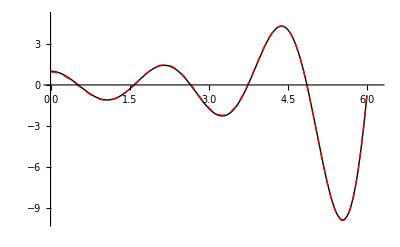

```mathematica
b=2.0;
ν=12.5;
Berry3a1=Plot[{Re[𝔹[x,ν,b]]},{x,0,6},PlotRange->{{0,6.2},{-10,5}},PlotStyle->{Black,Thick}];
Berry3aa1=Plot[Re[𝔹[x,ν,b]ℰ[x,ν,b]],{x,0,6},PlotRange->{{0,6.2},{-10,5}},PlotStyle->{Red,Dashed,Thick}];
Show[Berry3a1,Berry3aa1]
```

#### Figure 11b

```mathematica
b=2.0;
ν=12.5;
Berry3b1=Plot[{Re[𝔹[x,ν,b]]},{x,40,46}];
ExactDataPoints3b=Table[{40+n/2,Re[𝔹[40+n/2,ν,b]ℰ[40+n/2,ν,b]]},{n,0,12}];
Berry3b2=ListPlot[ExactDataPoints3b,PlotStyle->{PointSize[Large]}];
Show[Berry3b1,Berry3b2]
```

-Graphics-

#### Figure 11c

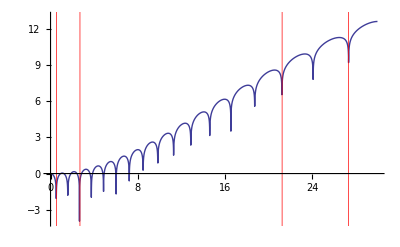

```mathematica
b=2.0;
ν=12.5;
Plot[Log[10,Abs[Re[𝔹[x,ν,b]]]],{x,0,30},
PlotRange->{{0,30},{-4,13}},PlotStyle->Thick,
GridLines->{{0.55,2.70,21.25,27.35},{}},
GridLinesStyle->Directive[Red]]
```